```mathematica
Clear["Global`*"];
SeedRandom[0];
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<"Sampler1`";
```

```mathematica
σ=0.00001;
```

```mathematica
SIGMA={{σ^2,0},{0,1}};
```

```mathematica
U[x_,y_]=1/2 Simplify[{x,y}.LinearSolve[SIGMA,{x,y}]];
```

```mathematica
dU[x_,y_]=GradientG[U[x,y],{x,y}];
```

```mathematica
ddU[x_,y_]=HessianH[U[x,y],{x,y}];
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{1.×10^10,0.},{0.,1.}} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

501 598.157 8.76351 0.749833 0.359902 10.3731 608.53 561.946 8.01795×10^-8 0.00547637 True {1,2,3,11} {1,11}

1002 425.705 3.39845 0.725085 0.400605 15.3113 329.483 441.017 2.51638×10^-7 0.0171872 False {1,4,8,9,11} {1,11}

1503 259.44 5.2247 0.492595 0.395217 9.98248 269.423 334.768 2.76801×10^-7 0.0142043 True {1,2,11} {1,11}

2004 329.966 7.0818 0.513181 0.369504 4.80237 323.643 334.768 2.51638×10^-7 0.0171872 False {1,3,5,11} {1,11}

2505 333.616 8.69262 0.53872 0.382624 21.5845 355.2 334.768 2.07965×10^-7 0.0251638 True {1,11} {1,11}

3006 320.49 2.19425 0.597418 0.414838 14.2785 385.811 334.768 2.51638×10^-7 0.0251638 False {1,2,7,9,11} {1,11}

3507 376.859 14.0799 0.501441 0.41849 10.7027 387.561 328.603 2.07965×10^-7 0.0207965 True {1,2,11} {1,11}

4008 204.358 2.52341 0.714161 0.284769 6.08606 393.012 210.444 2.28762×10^-7 0.0171872 False {1,6,7,11} {1,11}

4509 382.085 16.6652 0.661006 0.436924 10.9265 393.012 230.621 3.04482×10^-7 0.0276801 True {1,3,4,7,9,11} {1,11}

5010 220.849 3.49019 0.601777 0.354321 9.77224 312.22 230.621 2.51638×10^-7 0.0207965 False {1,4,5,9,11} {1,11}

5511 301.788 10.9212 0.659112 0.398762 10.4319 312.22 230.621 2.51638×10^-7 0.0207965 True {1,2,7,10,11} {1,11}

6012 222.351 2.31813 0.50567 0.26934 8.2706 312.22 230.621 2.51638×10^-7 0.0207965 False {1,3,4,5,11} {1,11}

6513 304.269 12.5209 0.633285 0.365579 7.95127 312.22 230.621 2.51638×10^-7 0.0207965 True {1,3,5,7,11} {1,11}

7014 224.92 5.46178 0.663041 0.406616 5.70116 312.22 230.621 2.51638×10^-7 0.0207965 False {1,2,4,7,11} {1,11}

7515 303.067 5.90574 0.601437 0.381838 9.1532 312.22 230.621 2.51638×10^-7 0.0207965 True {1,2,3,11} {1,11}

8016 221.145 6.09734 0.635815 0.435143 9.47666 312.22 230.621 2.51638×10^-7 0.0207965 False {1,2,10,11} {1,11}

8517 301.226 8.94627 0.727206 0.346437 10.9942 312.22 230.621 2.51638×10^-7 0.0207965 True {1,3,11} {1,11}

9018 221.171 2.51833 0.641903 0.439216 9.45034 312.22 230.621 2.51638×10^-7 0.0207965 False {1,4,11} {1,2,11}

9519 307.152 7.45482 0.511136 0.418611 5.06824 312.22 230.621 2.51638×10^-7 0.0207965 True {1,5,8,11} {1,11}

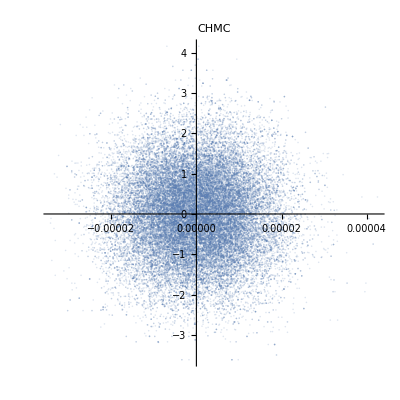

```mathematica
QS=hmc[U,dU,ddU,2,5000,10000,True,True];
ListPlot[QS,PlotLabel->CHMC,PlotStyle->Opacity[.2],AspectRatio->1]
```

```mathematica
StandardDeviation[QS]
```

{9.54222×10^-6,1.00718}

501 763.165 7.26342 0.511208 0.31848 9.37646 772.541 2.3421×10^10 1.71872×10^-7 0.0001 True {1,3,4,11} {1,11}

1002 759.564 7.83749 0.50102 0.456444 11.0835 770.648 2.3421×10^10 1.71872×10^-7 0.0001 True {1,4,7,11} {1,3,11}

1503 789.42 11.4485 0.536803 0.451005 10.5646 799.985 2.3421×10^10 2.07965×10^-7 0.0001 True {1,2,7,9,11} {1,11}

2004 726.057 12.2225 0.639128 0.378344 10.0952 736.152 2.3421×10^10 1.2913×10^-7 0.0001 True {1,3,6,11} {1,11}

2505 741.499 8.66174 0.684489 0.321843 9.67911 751.178 2.3421×10^10 1.42043×10^-7 0.0001 True {1,2,3,11} {1,11}

3006 722.649 7.72373 0.731945 0.398761 14.4117 737.061 2.3421×10^10 1.89059×10^-7 0.0001 True {1,2,7,9,11} {1,11}

3507 725.317 7.97046 0.554367 0.41399 11.7434 737.061 2.3421×10^10 1.71872×10^-7 0.0001 True {1,5,11} {1,11}

4008 725.455 12.9335 0.286227 0.280241 10.5304 735.985 2.3421×10^10 1.89059×10^-7 0.0001 True {1,2,11} {1,11}

4509 671.71 7.77287 0.499364 0.433683 14.1972 685.907 2.3421×10^10 1.89059×10^-7 0.0001 True {1,4,11} {1,11}

5010 675.455 21.2724 0.593059 0.370953 10.4526 685.907 2.3421×10^10 1.56247×10^-7 0.0001 True {1,3,9,11} {1,11}

5511 674.331 7.78507 0.550947 0.386992 11.5768 685.907 2.3421×10^10 1.56247×10^-7 0.0001 True {1,3,7} {1,11}

6012 676.395 7.21309 0.577442 0.375098 9.51198 685.907 2.3421×10^10 1.56247×10^-7 0.0001 True {1,2,4,6,11} {1,11}

6513 670.625 10.6078 0.664221 0.38787 15.282 685.907 2.3421×10^10 1.56247×10^-7 0.0001 True {1,4,5,8,10,11} {1,11}

7014 675.387 9.76882 0.617013 0.472913 10.5204 685.907 2.3421×10^10 1.56247×10^-7 0.0001 True {1,6,9,11} {1,11}

7515 676.034 7.825 0.553399 0.404299 9.87326 685.907 2.3421×10^10 1.56247×10^-7 0.0001 True {1,11} {1,11}

8016 674.459 12.0689 0.569938 0.428768 11.4489 685.907 2.3421×10^10 1.56247×10^-7 0.0001 True {1,2,11} {1,11}

8517 675.039 7.60714 0.560111 0.3716 10.8681 685.907 2.3421×10^10 1.56247×10^-7 0.0001 True {1,2,3,11} {1,11}

9018 670.435 14.2555 0.734036 0.418992 15.4722 685.907 2.3421×10^10 1.56247×10^-7 0.0001 True {1,3,5,6,9,11} {1,11}

9519 674.11 7.90029 0.656504 0.362926 11.7976 685.907 2.3421×10^10 1.56247×10^-7 0.0001 True {1,3,6,11} {1,11}

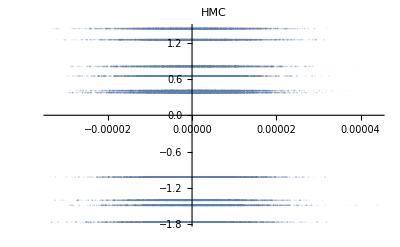

```mathematica
QS=hmc[U,dU,ddU,2,5000,10000,True,False];
ListPlot[QS,PlotLabel->HMC,PlotStyle->Opacity[.1]]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{1.×10^10,0.},{0.,1.}} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

501 1.06081×10^11 4.67316 0.4 0.516398 2.68614×10^10 7.20805×10^10 1.32943×10^11 1.×10^-9 0.00728905 False {1,2,5,6,11} {1,2,11}

1002 5.12588×10^10 4.9463 0.1 0.316228 4.20191×10^9 7.20805×10^10 5.54607×10^10 1.×10^-9 0.0106719 False {1,2,3,11} {2,11}

1503 1.61156×10^10 5.2651 0.3 0.483046 1.92226×10^9 7.20805×10^10 1.80379×10^10 1.×10^-9 0.00547637 False {1,3,4,11} {1,11}

2004 8.23887×10^9 6.18254 0.4 0.516398 9.71534×10^8 7.20805×10^10 9.2104×10^9 1.×10^-9 0.00728905 False {1,3,6,11} {1,2,11}

2505 3.79707×10^9 0.953168 0.3 0.483046 5.10033×10^8 7.20805×10^10 4.30711×10^9 1.×10^-9 0.00728905 False {1,3,4,11} {1,11}

3006 1.50636×10^9 2.44558 0.3 0.483046 1.89009×10^8 7.20805×10^10 1.69537×10^9 1.×10^-9 0.00662641 False {1,2,3,6,9,11} {1,4,11}

3507 7.72733×10^8 4.29457 0.2 0.421637 8.31849×10^7 7.20805×10^10 8.55918×10^8 1.×10^-9 0.00881975 False {1,2,3,5,11} {1,11}

4008 2.99326×10^8 9.85125 0.1 0.316228 2.83482×10^7 7.20805×10^10 3.27674×10^8 1.×10^-9 0.00602401 False {1,2,3,11} {1,11}

4509 1.4875×10^8 6.40096 0.2 0.421637 1.62589×10^7 7.20805×10^10 1.65009×10^8 1.×10^-9 0.00662641 False {1,5,11} {1,11}

5010 9.02238×10^7 2.72573 0.3 0.483046 7.68302×10^6 7.20805×10^10 9.79069×10^7 1.×10^-9 0.00662641 False {1,2,3,6,11} {1,5,11}

5511 2.59494×10^7 3.17799 0.3 0.483046 3.27462×10^6 7.20805×10^10 2.92241×10^7 1.×10^-9 0.00602401 False {1,3,4,11} {1,11}

6012 1.5943×10^7 5.95148 0.3 0.483046 1.62811×10^6 7.20805×10^10 1.75712×10^7 1.×10^-9 0.00728905 False {1,3,4,5,11} {1,3,11}

6513 6.05732×10^6 4.49823 0.3 0.483046 729383. 7.20805×10^10 6.78671×10^6 1.×10^-9 0.00662641 False {1,2,7,11} {1,5,6,11}

7014 3.70492×10^6 4.11502 0.4 0.516398 355180. 7.20805×10^10 4.0601×10^6 1.×10^-9 0.00662641 False {1,3,6,11} {1,11}

7515 1.51093×10^6 7.47967 0.400071 0.516337 216415. 7.20805×10^10 1.72735×10^6 1.×10^-9 0.00497852 False {1,3,11} {1,5,11}

8016 968083. 5.64104 0.4 0.516398 82122.6 7.20805×10^10 1.05021×10^6 1.×10^-9 0.0106719 False {1,2,8,9,11} {1,5,11}

8517 304114. 5.22481 0.4 0.516398 35012.9 7.20805×10^10 339127. 1.×10^-9 0.00547637 False {1,4,7,11} {1,11}

9018 166878. 3.66858 0.201814 0.420719 19879.3 7.20805×10^10 186758. 1.×10^-9 0.00452593 False {1,2,3,5,11} {1,11}

9519 119774. 5.20405 0.356982 0.476809 13539.2 7.20805×10^10 133313. 1.×10^-9 0.00547637 False {1,3,6,10,11} {1,4,7,11}

10020 78155.3 2.71109 0.570596 0.499174 8683.35 7.20805×10^10 86838.7 1.×10^-9 0.00452593 False {1,2,6,11} {1,2,11}

10521 51680.4 5.27323 0.300333 0.482817 5096.54 7.20805×10^10 56777. 1.×10^-9 0.00662641 False {1,2,3,11} {1,11}

11022 33975.9 1.72858 0.208416 0.417924 2947.95 7.20805×10^10 36923.8 1.×10^-9 0.00452593 False {1,2,7,11} {1,11}

11523 28941.5 15.3398 0.331929 0.430135 2004.74 7.20805×10^10 30946.2 1.×10^-9 0.00340039 False {1,2,5,10,11} {1,4,11}

12024 29346. 7.75941 0.484096 0.499559 1600.25 7.20805×10^10 30946.2 1.×10^-9 0.00374043 False {1,3,8,9,11} {1,11}

12525 27003.8 8.23701 0.575853 0.458373 1269.16 7.20805×10^10 28273. 1.×10^-9 0.00232252 False {1,2,5,11} {1,4,11}

13026 27268.7 3.68067 0.379942 0.359111 1004.27 7.20805×10^10 28273. 1.×10^-9 0.00340039 False {1,2,6} {11}

13527 27449.9 6.74208 0.574993 0.444514 823.105 7.20805×10^10 28273. 1.×10^-9 0.00211138 False {1,3,4,5,10,11} {1,11}

14028 27564.8 2.07571 0.463804 0.431519 708.157 7.20805×10^10 28273. 1.×10^-9 0.00232252 False {1,3,4,6,11} {1,7,11}

14529 27688.9 10.8314 0.488827 0.469292 584.077 7.20805×10^10 28273. 1.×10^-9 0.00281024 False {1,7,10,11} {1,11}

15030 27807.2 6.01452 0.239171 0.271146 465.757 7.20805×10^10 28273. 1.×10^-9 0.00255477 False {1} {11}

15531 27884.4 3.25189 0.621983 0.442469 388.582 7.20805×10^10 28273. 1.×10^-9 0.00255477 False {1,4,7,9,11} {1,11}

16032 27949. 4.95541 0.52729 0.412508 323.917 7.20805×10^10 28273. 1.×10^-9 0.00255477 False {1,2,3,5,8,11} {1,11}

16533 28002.4 3.37436 0.6089 0.425347 270.606 7.20805×10^10 28273. 1.×10^-9 0.00255477 False {1,3,4,11} {1,11}

17034 28049. 6.57248 0.334863 0.326847 223.955 7.20805×10^10 28273. 1.×10^-9 0.00255477 False {1,4,5,11} {1,11}

17535 28083.3 5.46655 0.489537 0.385525 189.709 7.20805×10^10 28273. 1.×10^-9 0.00255477 False {1,5,6,11} {1,11}

18036 28112. 5.52897 0.648744 0.458781 160.927 7.20805×10^10 28273. 1.×10^-9 0.00255477 False {1,7,11} {1,5,11}

18537 28133.8 3.63158 0.331259 0.463144 139.13 7.20805×10^10 28273. 1.×10^-9 0.00255477 False {1,4,11} {1,11}

19038 28160.6 4.20301 0.650364 0.414513 112.348 7.20805×10^10 28273. 1.×10^-9 0.00255477 False {1,4,6,8,9,11} {1,11}

19539 28175. 4.54233 0.614635 0.361896 97.9988 7.20805×10^10 28273. 1.×10^-9 0.00255477 False {1,2,3,4,11} {1,11}

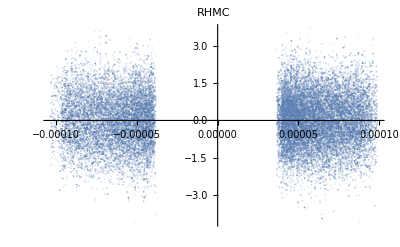

```mathematica
QS=hmc[U,dU,ddU,2,15000,20000,False,False];
ListPlot[QS,PlotLabel->RHMC,PlotStyle->Opacity[.2]]
```